## Notebook Basics

Input cells contain commands. Text, Section, etc.  cells contain words etc. In addition to computing things Mathematica also typesets equations etc.

⇧⌤ executes commands in an Input cell.

Square braces (on the far side) let you select a cell or group of cells

## Mathematica Basics

Commands are case sensitive.  Function arguments are enclosed by “[ ]”. Output is suppressed with “;” s

⇧⌤ executes commands

Commands usually tell you exactly what they do. For suitable matrices A and vectors b

“MatrixPlot[A]” and “ListPlot[b]” draw standard pictures.

“x=LinearSolve[A, b]”  computes a vector x satisfying A x=b.

“{λ,V}=Eigensystem[A]”  gives lists of eigenvalues λ_1,λ_2… and eigenvectors v_1,v_2,… satisfying A v_i=λ_i v_i.

We are going to learn what (and a tiny bit of how) these commands do.

### Eigenstuff

The following cell imports a matrix “A” from a NIST repository, plots the matrix, computes eigenstuff and of the matrix and plots the eigenvalues on a log scale.  The origin of the matrix is described at https://math.nist.gov/MatrixMarket/data/Harwell-Boeing/bcsstruc2/bcsstk14.html

SparseArray[…]

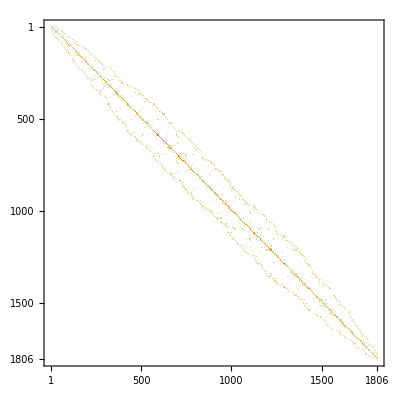

Eigensystem::arh: Because finding 1806 out of the 1806 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

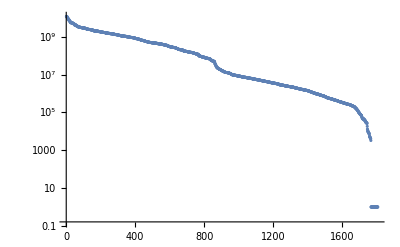

```mathematica
A=Import[
"https://math.nist.gov/pub/MatrixMarket2/Harwell-Boeing/bcsstruc2/bcsstk14.mtx.gz"]
MatrixPlot[A]
{λ,V}=Eigensystem[A];
ListLogPlot[λ,PlotRange->All,GridLines->Automatic]
```

### LinearSolve

The following cell imports a matrix “A” from a NIST repository, plots the matrix and demonstrates LinearSolve.  The origin of the matrix is described at
https://math.nist.gov/pub/MatrixMarket2/Harwell-Boeing/bcsstruc3/bcsstk24.html

```mathematica
A=Import[
"https://math.nist.gov/pub/MatrixMarket2/Harwell-Boeing/bcsstruc3/bcsstk24.mtx.gz"];
MatrixPlot[A];
{m,n}=Dimensions[A];
xIn=Cos[Range[0.0,π,π/(n-1)]];
b=A.xIn;
xOut=LinearSolve[A,b];
TabView[{"x_in"->ListPlot[xIn],"b"->ListPlot[b],"x_Out"->ListPlot[xOut],
"x_in-x_Out"->ListPlot[xIn-xOut,PlotRange->All]}]
```

1234

### Matrix and Vector Arithmetic

```mathematica
{m,n}={4,3};
A1=RandomReal[{-1,1},{m,m}];
A2=RandomReal[{-1,1},{m,n}];
A3=RandomReal[{-1,1},{n,n}];
A4=RandomReal[{-1,1},{n,n}];
x=RandomReal[{-1,1},n];
Map[Dimensions,{A1,A2,A3,A4,x}]
Map[MatrixForm,{A1,A2,A3,A4}]
```

{{4,4},{4,3},{3,3},{3,3},{3}}

{(0.720135 | -0.752619 | 0.372386 | -0.0163861
-0.764078 | -0.542639 | -0.286185 | -0.645228
-0.582479 | 0.308648 | -0.970005 | -0.744544
-0.660337 | -0.19443 | -0.804185 | 0.564911),(-0.447166 | 0.714993 | -0.0628722
-0.361247 | -0.455616 | -0.526199
-0.147894 | -0.176602 | -0.502366
-0.10463 | -0.363756 | -0.230259),(-0.771541 | -0.592521 | -0.141283
0.112865 | 0.0180059 | -0.682132
0.427302 | 0.334773 | 0.0568937),(-0.789303 | 0.642969 | 0.287227
-0.832707 | -0.0646091 | -0.231733
0.542562 | 0.888701 | 0.27128)}